Here it is made the graphs of colony for the auto-activated system

## Parameters

```mathematica
(*Values of knetic parameters*)
```

```mathematica
kgs=Range[0.01,1,0.02];
γgs=Range[0.02,2,0.04];(* 0.02-0.18, 0.22-0.38, 0.42-0.58, 0.62-0.78, 0.82-0.98, 1.02-1.18, 1.22-1.38, 1.42-1.58, 1.62-1.78, 1.82-1.98 *)
γms=Range[0.001,0.1(*name*),0.002];(* 0.001-0.009, 0.011-0.019, 0.021-0.029, 0.031-0.039,0.041-0.049, 0.051-0.059, 0.061-0.069, 0.071-0.079,0.081-0.089, 0.091-0.099 *)
γps=Range[0.001,0.1(*name*),0.002];
(* 0.001-0.009, 0.011-0.019, 0.021-0.029, 0.031-0.039,0.041-0.049, 0.051-0.059, 0.061-0.069, 0.071-0.079,0.081-0.089, 0.091-0.099 *)
```

```mathematica
(*Values of diffusion and colony sizes -radius-*)
```

```mathematica
dfs=Range[0.01,0.1,0.01];
sizes={2,5,10,15,20,25};
```

```mathematica
(*Iterations and replicates*)
```

```mathematica
iteraciones=500;
replicas=5;
```

```mathematica
(*parameters labels*)
```

```mathematica
aparametro1="_kg";
aparametro2="_γg";
```

```mathematica
bparametro1="_γg";
bparametro2="_γm";
```

```mathematica
cparametro1="_γm";
cparametro2="_γp";
```

## Graphs for kinetic parameters

```mathematica
SetDirectory["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/4multiNoiseCommunityE/outData"]
```

/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/4multiNoiseCommunityE/outData

```mathematica
data1=Table[Import["bRCLEcolony"<>aparametro1<>ToString[kg]<>aparametro2<>ToString[γg]<>"_todos","CSV"],{kg,kgs},{γg,γgs}];
```

```mathematica
data1=Table[Import["bRCLEcolony"<>bparametro1<>ToString[γg]<>bparametro2<>ToString[γm]<>"_todos","CSV"],{γg,γgs},{γm,γms}];
```

```mathematica
data1=Table[Import["bRCLEcolony"<>cparametro1<>ToString[γm]<>cparametro2<>ToString[γp]<>"_todos","CSV"],{γm,γms},{γp,γps}];
```

```mathematica
(***********************************Veify the correct Import of data*)
```

```mathematica
data1//Dimensions
```

{50,50,5}

```mathematica
data1[[1,1]]
```

```mathematica
Table[data1[[i]]//Length,{i,50}]
```

{50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50}

```mathematica
Count[Flatten[data1],$Failed]
```

0

```mathematica
(**********************************Getting the estimates FF and Mean*)
```

```mathematica
{meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep}=Table[Map[Flatten,data1[[All,All,i]]],{i,4}];
```

```mathematica
(****************************************************)
modelo=" One Gen R burstmRNA CLE";
```

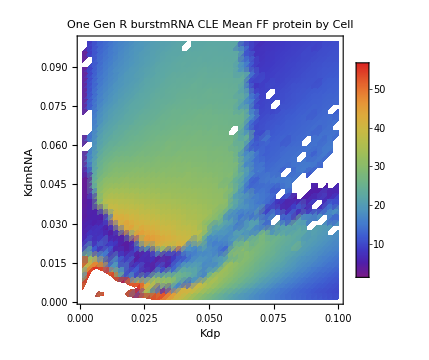
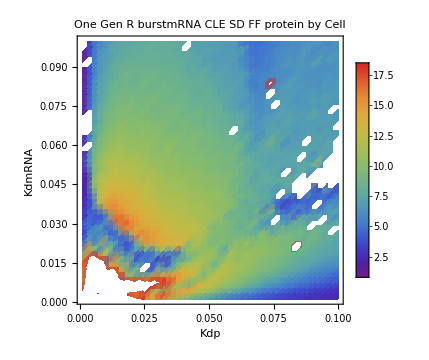
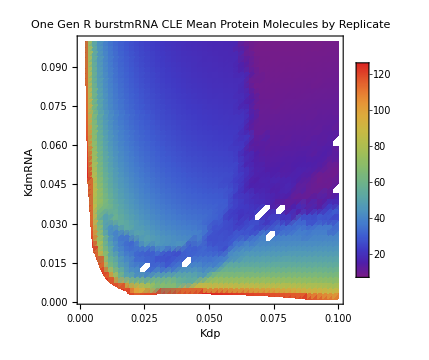
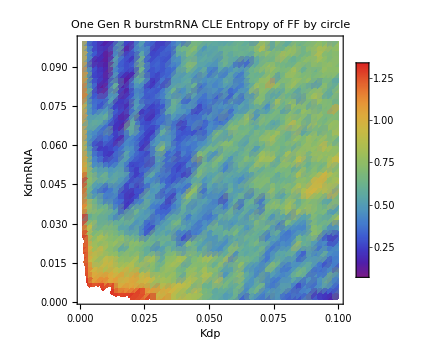

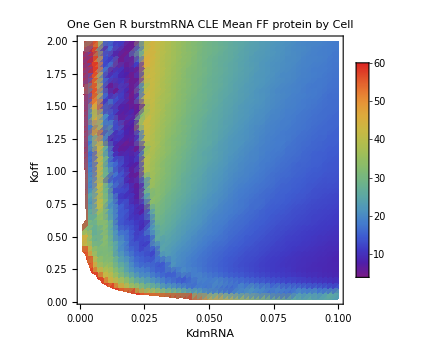
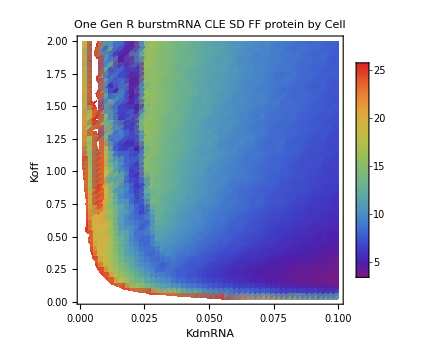
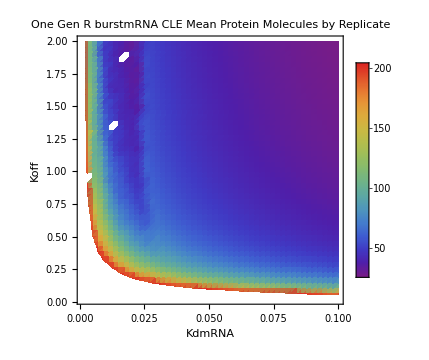
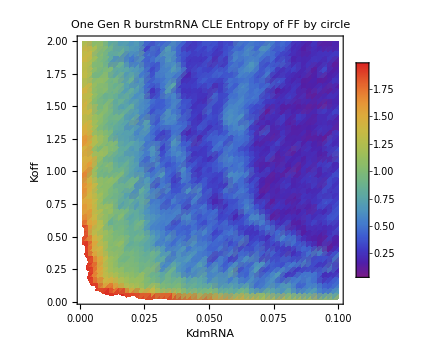

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.001,0.1},{0.001,0.1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},ColorFunction->"Rainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black, 17],LabelStyle->Directive[Black,20]],{i,{{meanFFbyCell,ToString[modelo]<>" \n Mean FF protein by Cell"},{sdFFbyCell,ToString[modelo]<>" \n SD FF protein by Cell"},{meanMoleculesrep,ToString[modelo]<>" \n  Mean Protein Molecules by Replicate"},{meanEntoripasRep,ToString[modelo]<>" \n Entropy of FF by circle"}}}]
```

```mathematica
(**************************ENTROPY*)
```

```mathematica
meanEntoripasRepkoff=meanEntoripasRep;
```

```mathematica
meanEntoripasRepkdm=meanEntoripasRep;
```

```mathematica
meanEntoripasRepkdp=meanEntoripasRep;
```

```mathematica
meanEntoripasRepkdp[[1,10]]=2.25;meanEntoripasRepkoff[[1,10]]=2.25;meanEntoripasRepkdm[[1,10]]=2.25;
```

```mathematica
meanEntoripasRepkdp[[1,1]]=0;meanEntoripasRepkoff[[1,1]]=0;meanEntoripasRepkdm[[1,1]]=0;
```

```mathematica
meanEntoripasRepkoff[[1,10]]
```

0.780261

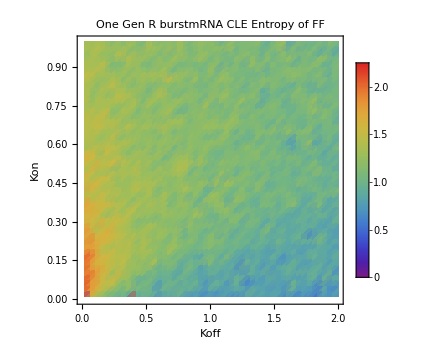
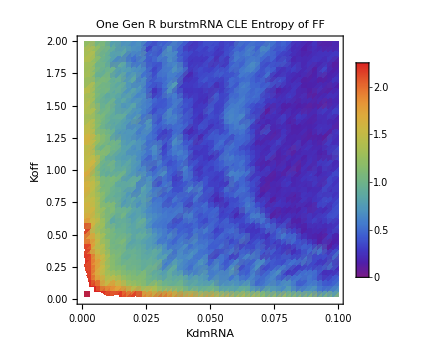
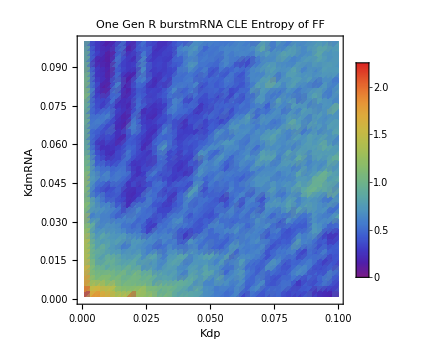

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->i[[3]](*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->i[[4]],PlotRange->{0,2.25},ColorFunction->"Rainbow",ImageSize->Medium],{i,{{meanEntoripasRepkoff,ToString[modelo]<>" \n Entropy of FF  ",{"Koff","Kon"},{{0.02,2},{0.01,1}}},{meanEntoripasRepkdm,ToString[modelo]<>" \n Entropy of FF",{"KdmRNA","Koff"},{{0.001,0.1},{0.02,2}}},{meanEntoripasRepkdp,ToString[modelo]<>" \n  Entropy of FF" , {"Kdp","KdmRNA"},{{0.001,0.1},{0.001,0.1}}}}}]
```

```mathematica
(**************************FF*)
```

```mathematica
meanRepFFByCirclekdp=data1[[All,All,5]];(*FF by circle*)
ffProteinkdp=meanRepFFByCirclekdp[[All,All,13]];(*FF from the last circle- the whole colony*)
Table[If[Head[ffProteinkdp[[j,i]]]===String,ffProteinkdp[[j,i]]=ffProteinkdp[[j,i-1]],ffProteinkdp[[j,i]]=ffProteinkdp[[j,i]]],{j,50},{i,50}];(*To take off white spots*)
```

```mathematica
meanRepFFByCirclekdm=data1[[All,All,5]];
ffProteinkdm=meanRepFFByCirclekdm[[All,All,13]];
Table[If[Head[ffProteinkdm[[j,i]]]===String,ffProteinkdm[[j,i]]=ffProteinkdm[[j,i-1]],ffProteinkdm[[j,i]]=ffProteinkdm[[j,i]]],{j,50},{i,50}];(*para quitar los parches blancos*)
```

```mathematica
meanRepFFByCirclekoff=data1[[All,All,5]];
ffProteinkoff=meanRepFFByCirclekoff[[All,All,13]];
Table[If[Head[ffProteinkoff[[j,i]]]===String,ffProteinkoff[[j,i]]=ffProteinkoff[[j,i-1]],ffProteinkoff[[j,i]]=ffProteinkoff[[j,i]]],{j,50},{i,50}];(*para quitar los parches blancos*)
```

```mathematica
ffProteinkdp[[1,1]]=1;ffProteinkdm[[1,1]]=1;ffProteinkoff[[1,1]]=1;
ffProteinkdp[[1,10]]=50;ffProteinkdm[[1,10]]=50;ffProteinkoff[[1,10]]=50;
```

```mathematica
ffProteinkdp[[1,2]]=1;ffProteinkdm[[1,2]]=1;ffProteinkoff[[1,2]]=1;
ffProteinkdp[[1,11]]=50;ffProteinkdm[[1,11]]=50;ffProteinkoff[[1,11]]=50;
```

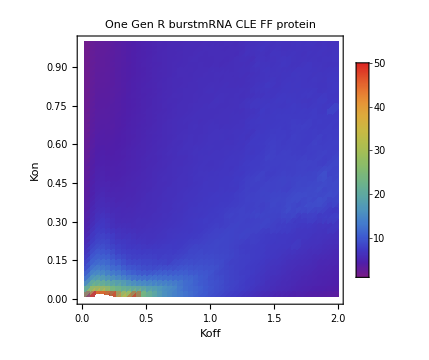
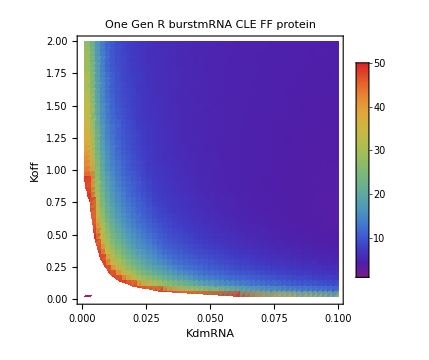
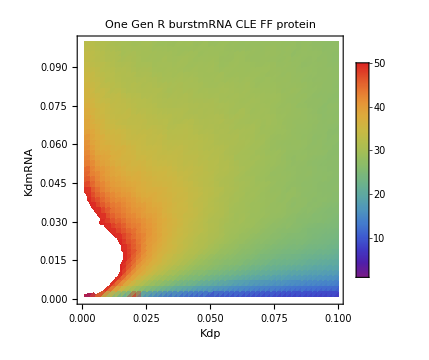

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->i[[3]](*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->i[[4]],PlotRange->{1,50},ColorFunction->"Rainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black, 20],LabelStyle->Directive[Black,14]],{i,{{ffProteinkoff,ToString[modelo]<>" \n  FF protein",{"Koff","Kon"},{{0.02,2},{0.01,1}}},{ffProteinkdm,ToString[modelo]<>" \n  FF protein ",{"KdmRNA","Koff"},{{0.001,0.1},{0.02,2}}},{ffProteinkdp,ToString[modelo]<>" \n   FF protein", {"Kdp","KdmRNA"},{{0.001,0.1},{0.001,0.1}}}}}]
```

```mathematica
(**************************MEAN*)
```

```mathematica
meanMoleculesrepkoff=Map[Flatten,data1[[All,All,3]]];
Table[If[Head[meanMoleculesrepkoff[[j,i]]]===String,meanMoleculesrepkoff[[j,i]]=meanMoleculesrepkoff[[j,i-1]],meanMoleculesrepkoff[[j,i]]=meanMoleculesrepkoff[[j,i]]],{j,50},{i,50}];
```

```mathematica
meanMoleculesrepkdm=Map[Flatten,data1[[All,All,3]]];
Table[If[Head[meanMoleculesrepkdm[[j,i]]]===String,meanMoleculesrepkdm[[j,i]]=meanMoleculesrepkdm[[j,i-1]],meanMoleculesrepkdm[[j,i]]=meanMoleculesrepkdm[[j,i]]],{j,50},{i,50}];
```

```mathematica
meanMoleculesrepkdp=Map[Flatten,data1[[All,All,3]]];
Table[If[Head[meanMoleculesrepkdp[[j,i]]]===String,meanMoleculesrepkdp[[j,i]]=meanMoleculesrepkdp[[j,i-1]],meanMoleculesrepkdp[[j,i]]=meanMoleculesrepkdp[[j,i]]],{j,50},{i,50}];
```

```mathematica
meanMoleculesrepkoff[[1,1]]=10;meanMoleculesrepkdm[[1,1]]=10;meanMoleculesrepkdp[[1,1]]=10;
meanMoleculesrepkoff[[1,10]]=1950;meanMoleculesrepkdm[[1,10]]=1950;meanMoleculesrepkdp[[1,10]]=1950;
```

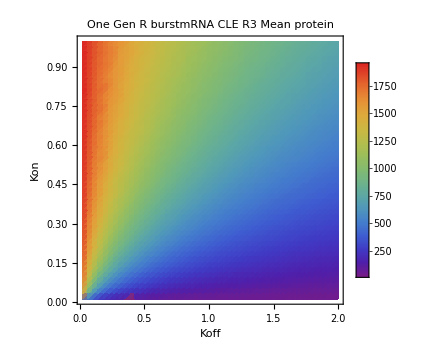
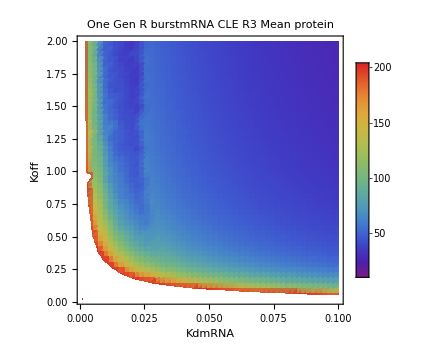
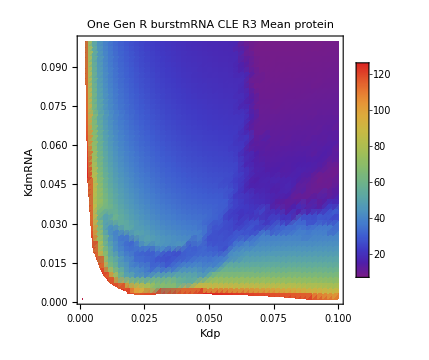

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->i[[3]](*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->i[[4]],ColorFunction->"Rainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black, 20],LabelStyle->Directive[Black,19]],{i,{{meanMoleculesrepkoff,ToString[modelo]<>" \n   Mean protein ",{"Koff","Kon"},{{0.02,2},{0.01,1}}},{meanMoleculesrepkdm,ToString[modelo]<>" \n  Mean protein ",{"KdmRNA","Koff"},{{0.001,0.1},{0.02,2}}},{meanMoleculesrepkdp,ToString[modelo]<>" \n Mean protein ", {"Kdp","KdmRNA"},{{0.001,0.1},{0.001,0.1}}}}}]
```

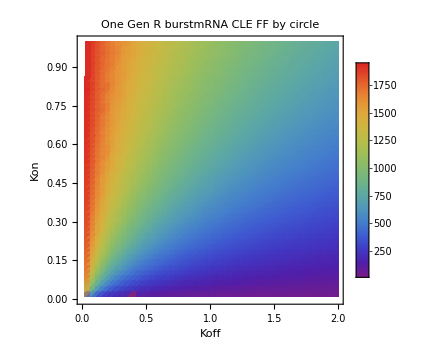
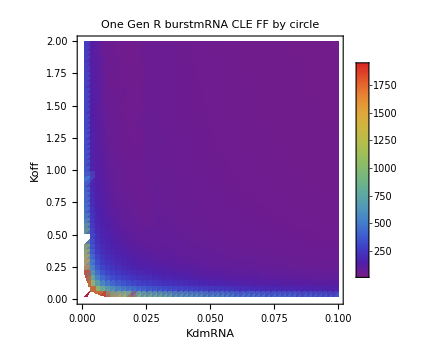
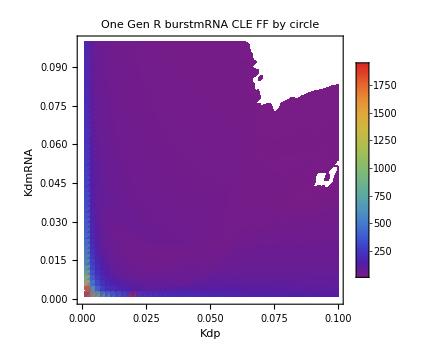

```mathematica
(*I you put the mean in the same scale for 3 plots : *****************************************)
```

## Graphs for uncoupled vs coupled

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS3-2/v2/data"];
```

```mathematica
data2=ToExpression@Table[Import["burstmRCLE_γg"<>i,"CSV"],{i,{"0.5","1.","1.5","2"}}];
```

```mathematica
data2=ToExpression@Table[Import["burstmRCLE_γm"<>i,"CSV"],{i,{"0.025","0.05","0.075","0.1"}}];
```

```mathematica
ffProtein2=Map[Flatten,Transpose[Map[Partition[#,25]&,data2[[All,2(*Protein*),All,1(*FF*)]]]]];
```

```mathematica
ffProtein2n=Map[#[[Range[1,100,2]]]&,ffProtein2[[Range[1,100,2]]]];
```

```mathematica
(******************************************2000 pts**********)
ffmRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,1(*FF*)]]]]];
cv2mRNA=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,1(*mRNA*),All,2(*cv2*)]]]]];
ffProtein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,1(*FF*)]]]]];
cv2Protein=Map[Flatten,Transpose[Map[Partition[#,5]&,data[[All,2(*Protein*),All,2(*cv2*)]]]]];
```

```mathematica
(**************************************************)
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS5/FeedBack/Koff"]
```

/media/lina/DATA/SimulacionesTesis/resultadosS5/FeedBack/Koff

```mathematica
data1=Table[Import["bRCLEcolony"<>parametro1<>ToString[kg]<>parametro2<>ToString[γg]<>"_todos","CSV"],{kg,kgs},{γg,γgs}];
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS5/FeedBack/Kdm"]
```

/media/lina/DATA/SimulacionesTesis/resultadosS5/FeedBack/Kdm

```mathematica
data1=Table[Import["bRCLEcolony"<>parametro1<>ToString[γg]<>parametro2<>ToString[γm]<>"_todos","CSV"],{γg,γgs},{γm,γms}];
```

```mathematica
SetDirectory["/media/lina/DATA/SimulacionesTesis/resultadosS5/FeedBack/Kdp"]
```

```mathematica
data1=Table[Import["bRCLEcolony"<>parametro1<>ToString[γm]<>parametro2<>ToString[γp]<>"_todos","CSV"],{γm,γms},{γp,γps}];
```

```mathematica
{meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep}=Table[Map[Flatten,data1[[All,All,i]]],{i,4}];
```

```mathematica
meanRepFFByCircle=data1[[All,All,5]];
```

```mathematica
ffProtein1=meanRepFFByCircle[[All,All,13]];
```

```mathematica
Table[If[Head[ffProtein1[[j,i]]]===String,ffProtein1[[j,i]]=ffProtein1[[j,i-1]],ffProtein1[[j,i]]=ffProtein1[[j,i]]],{j,50},{i,50}];
```

```mathematica
(****************************************************)
modelo1=" One R G Coupled ";
modelo2=" One R G Non-Coupled";
```

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Kdp","KdmRNA"}(*{"Koff","Kon"}{"KdmRNA","Koff"}{"Kdp","KdmRNA"}*),DataRange->{{0.02,2},{0.01,1}(*{0.001,0.1},{0.01,1}{0.02,2}*)},PlotRange-> {1,90},ColorFunction->"Rainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black, 14],LabelStyle->Directive[Black,20]],{i,{{ffProtein1,ToString[modelo1]<>" \n FF protein"},{ffProtein2,ToString[modelo2]<>" \n FF protein"}}}]
```

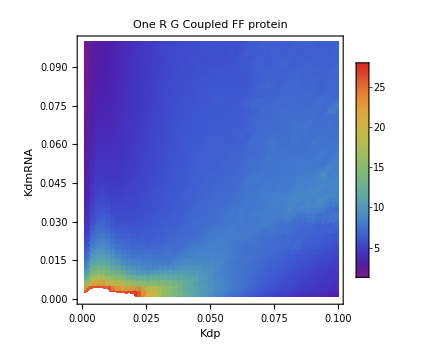
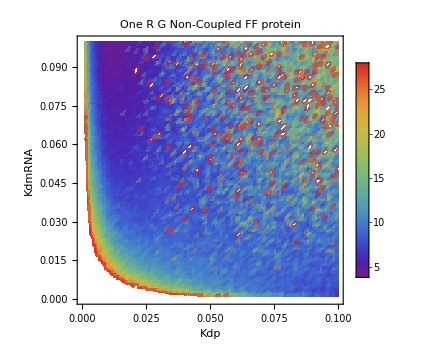

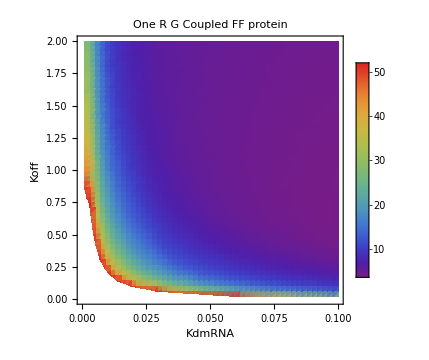
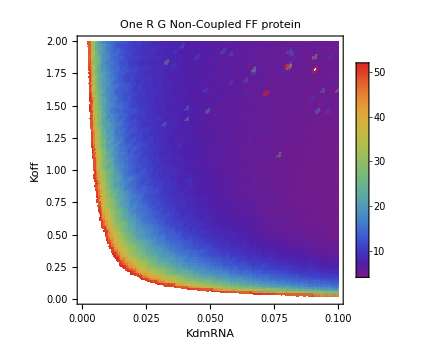

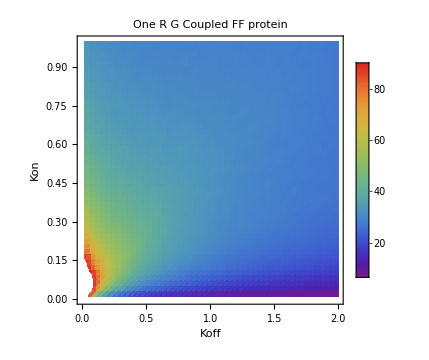
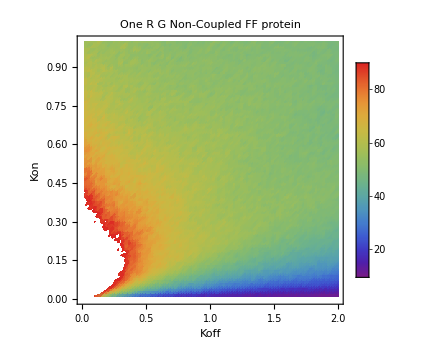

## Graphs for diffusion and colony size

```mathematica
SetDirectory["/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/4multiNoiseCommunityE/outData"]
```

/media/lina/DATA/noiseGRNdevelopmentLinaMRuizG_git/BiologicalNoise_DevelopmentalGeneRegulatoryNetworks/4multiNoiseCommunityE/outData

```mathematica
data1=Table[Import["bRCLEcolonyop2_"<>ToString[size]<>"_df:"<>ToString[df]<>"_todos","CSV"],{size,sizes},{df,dfs}];
```

```mathematica
(*op1: R1
op2: R2
op3: R4
op4: R3*)
```

```mathematica
(*******************Getting estimates*****************************************************+)
```

```mathematica
{meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep}=Table[Map[Flatten,data1[[All,All,i]]],{i,4}];
ffProtein1=data1[[All,All,5,-1]];
```

```mathematica
(**Taking off white spots***************************************)
```

```mathematica
meanMoleculesrep=Table[If[Head[meanMoleculesrep[[j,i]]]===String,meanMoleculesrep[[j,i]]=meanMoleculesrep[[j,i-1]],meanMoleculesrep[[j,i]]=meanMoleculesrep[[j,i]]],{j,6},{i,10}];meanFFbyCell=Table[If[Head[meanFFbyCell[[j,i]]]===String,meanFFbyCell[[j,i]]=meanFFbyCell[[j,i-1]],meanFFbyCell[[j,i]]=meanFFbyCell[[j,i]]],{j,6},{i,10}];
sdFFbyCell=Table[If[Head[sdFFbyCell[[j,i]]]===String,sdFFbyCell[[j,i]]=sdFFbyCell[[j,i-1]],sdFFbyCell[[j,i]]=sdFFbyCell[[j,i]]],{j,6},{i,10}];
meanMoleculesrep=Table[If[Head[meanMoleculesrep[[j,i]]]===String,meanMoleculesrep[[j,i]]=meanMoleculesrep[[j,i-1]],meanMoleculesrep[[j,i]]=meanMoleculesrep[[j,i]]],{j,6},{i,10}];ffProtein1=Table[If[Head[ffProtein1[[j,i]]]===String,ffProtein1[[j,i]]=ffProtein1[[j,i+1]],ffProtein1[[j,i]]=ffProtein1[[j,i]]],{j,5},{i,10}];
```

```mathematica
(****************************************************)
modelo=" One Gen R burstmRNA CLE R4";
```

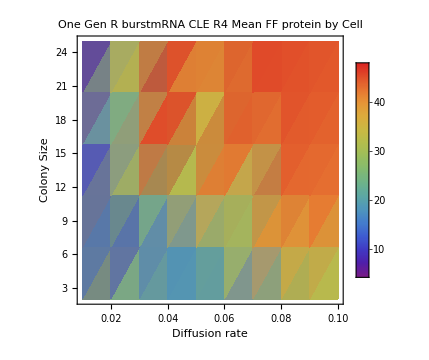
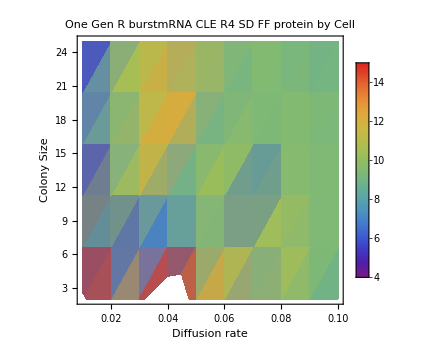
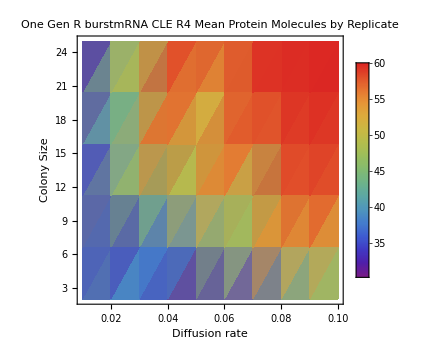
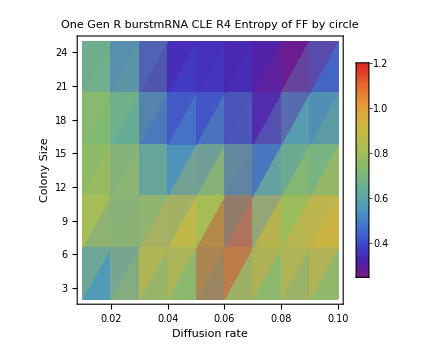
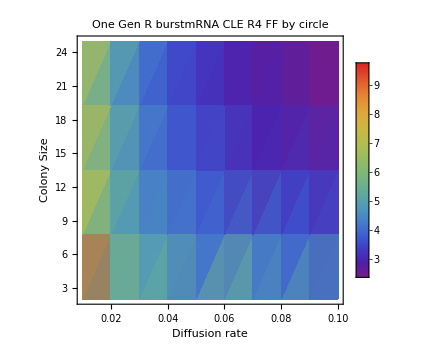

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Diffusion rate","Colony Size"},DataRange->{{0.01,0.1},{2,25}},ColorFunction->"Rainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black, 20],LabelStyle->Directive[Black,20]],{i,{{meanFFbyCell,ToString[modelo]<>" \n Mean FF protein by Cell"},
{sdFFbyCell,ToString[modelo]<>" \n SD FF protein by Cell"},
{meanMoleculesrep,ToString[modelo]<>" \n  Mean Protein Molecules by Replicate"},
{meanEntoripasRep,ToString[modelo]<>" \n Entropy of FF by circle"},
{ffProtein1,ToString[modelo]<>" \n FF by circle"}}}]
```

```mathematica
(**********************************************************************************************************************************************************)
(***SAME SCALE FOR R2-4*)
```

```mathematica
{meanFFbyCellop1,sdFFbyCellop1,meanMoleculesrepop1,meanEntoripasRepop1}={meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep};
meanRepFFByCircleop1=ffProtein1;
```

```mathematica
{meanFFbyCellop2,sdFFbyCellop2,meanMoleculesrepop2,meanEntoripasRepop2}={meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep};
meanRepFFByCircleop2=ffProtein1;
```

```mathematica
{meanFFbyCellop3,sdFFbyCellop3,meanMoleculesrepop3,meanEntoripasRepop3}={meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep};
meanRepFFByCircleop3=ffProtein1;
```

```mathematica
{meanFFbyCellop4,sdFFbyCellop4,meanMoleculesrepop4,meanEntoripasRepop4}={meanFFbyCell,sdFFbyCell,meanMoleculesrep,meanEntoripasRep};
meanRepFFByCircleop4=ffProtein1;
```

```mathematica
meanMoleculesrepop2[[1,1]]=meanMoleculesrepop2[[1,2]];
meanMoleculesrepop3[[1,1]]=meanMoleculesrepop3[[1,2]];
meanMoleculesrepop4[[1,1]]=meanMoleculesrepop4[[1,2]];
meanMoleculesrepop2[[1,10]]=meanMoleculesrepop2[[1,9]];
meanMoleculesrepop3[[1,10]]=meanMoleculesrepop3[[1,9]];
meanMoleculesrepop4[[1,10]]=meanMoleculesrepop4[[1,9]];
```

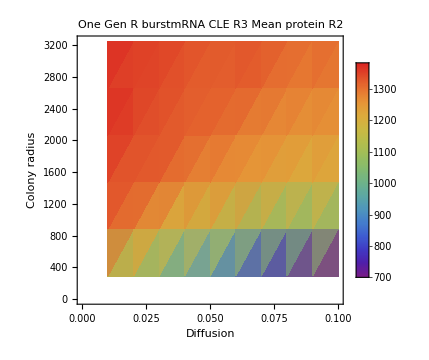
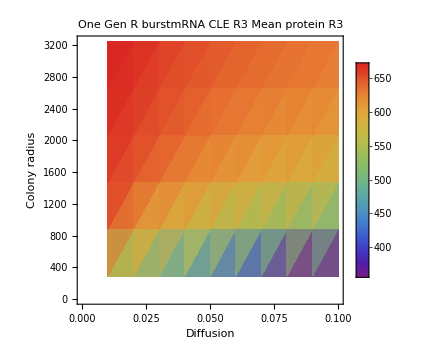
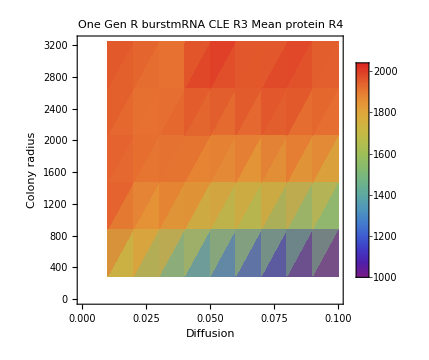

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotRange->{3,20000},PlotLegends->Automatic,Frame-> True,FrameLabel->{"Diffusion","Colony radius"},DataRange->{{0.01,0.1},{289,3249}},ColorFunction->"Rainbow",ImageSize->Medium,FrameTicksStyle->Directive[Black, 18],LabelStyle->Directive[Black,13]],
{i,{{meanMoleculesrepop2,ToString[modelo]<>" \n   Mean protein R2"},
{meanMoleculesrepop3,ToString[modelo]<>" \n  Mean protein R3"},
{meanMoleculesrepop4,ToString[modelo]<>" \n Mean protein R4"}}}]
```

```mathematica
meanRepFFByCircleop2[[1,1]]=10;
meanRepFFByCircleop3[[1,1]]=10;
meanRepFFByCircleop4[[1,1]]=10;
meanRepFFByCircleop2[[1,10]]=100;
meanRepFFByCircleop3[[1,10]]=100;
meanRepFFByCircleop4[[1,10]]=100;
```

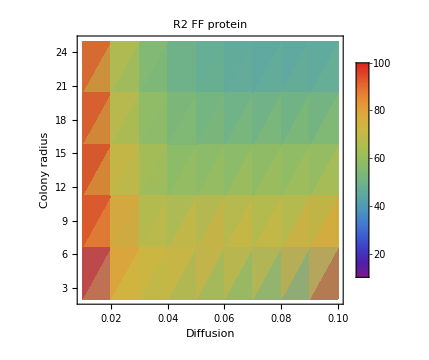
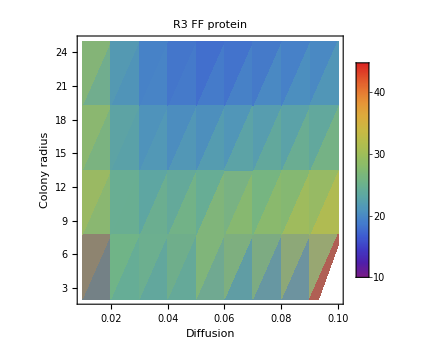
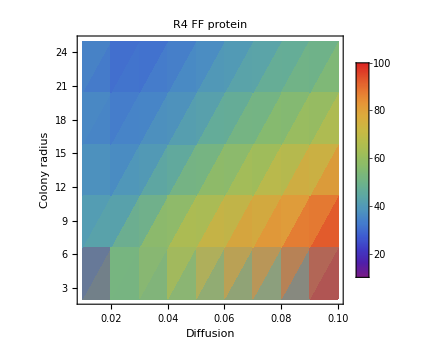

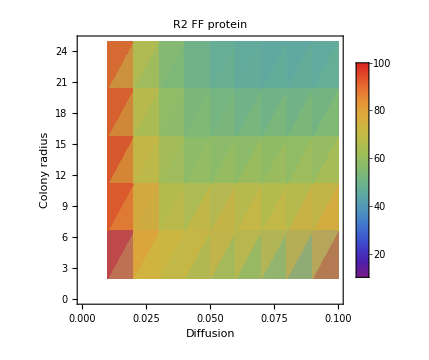
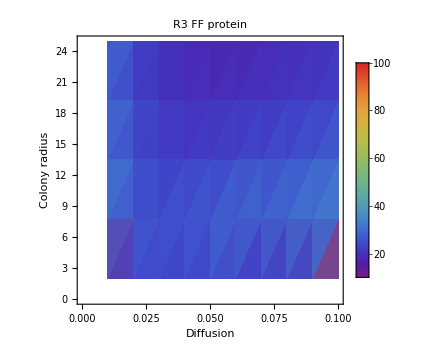
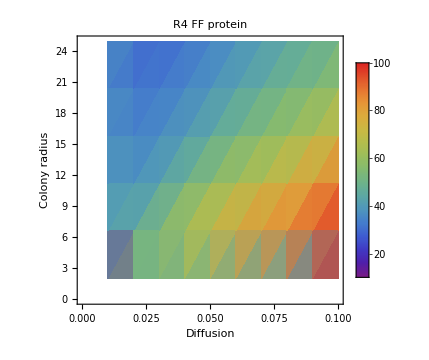

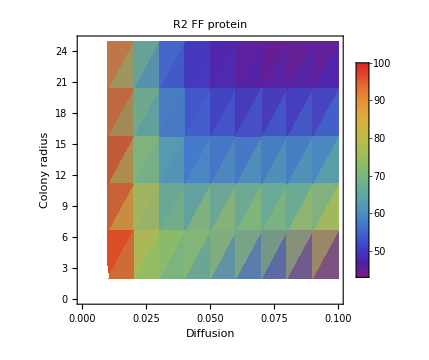
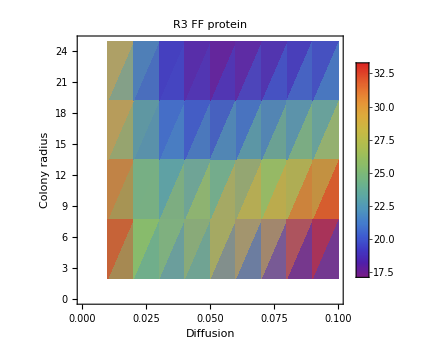

```mathematica
Table[ListDensityPlot[i[[1]],PlotLabel->i[[2]],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Diffusion","Colony radius"},DataRange->{{0.01,0.1},{2,25}},ColorFunction->"Rainbow",ImageSize->Medium],
{i,{
{meanRepFFByCircleop2," R2  FF protein "},
{meanRepFFByCircleop3," R3 FF protein "},
{meanRepFFByCircleop4," R4 FF protein "}}}]
```

```mathematica
(***********************************************************************************************************************************************************)
```

```mathematica
(*The FF from the whole colony is more different from FF of de rest (ie. the center of the colony) of the colony when the diffusion rate increase. But this effect is lower with the colony size increase *)
```

```mathematica
meanRepFFByCircle=data1[[All,All,5]];
```

```mathematica
meanRepFFByCircle[[5,5]]=Map[Mean,Transpose[{meanRepFFByCircle[[5,4]],meanRepFFByCircle[[5,6]]}]]
```

{2.21478,2.2884,2.48355,2.54674,2.65366,2.64937,2.63987,2.66772,2.69687,2.7344,2.73395,2.72932,2.73999,2.76333,2.7684,2.74504,2.73629,2.73886,2.73043,2.7312,2.73282,2.74565,2.78471,2.88514,3.18243}

```mathematica
(*plots*)
```

```mathematica
Table[ListLinePlot[Map[Transpose[{dfs,#}]&,Table[meanRepFFByCircle[[i,All,j]],{j,Length[meanRepFFByCircle[[i,1]]]}]],PlotLabel->"FF all colony by circle Tamaño: "<>ToString[i],PlotLegends->Automatic,Frame-> True,FrameLabel->{"Diffussion rate","FF by circle from center"},ImageSize->Medium,FrameTicksStyle->Directive[Black, 18],LabelStyle->Directive[Black,13]],{i,6}]
```

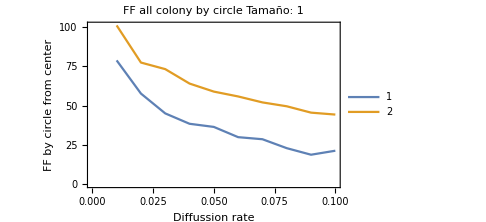
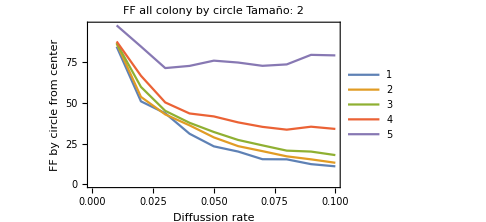
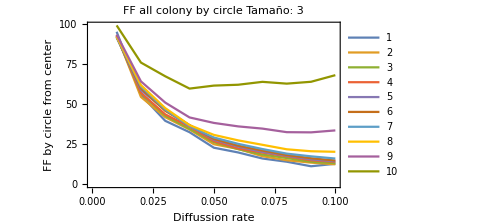
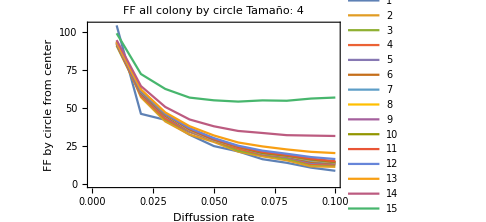
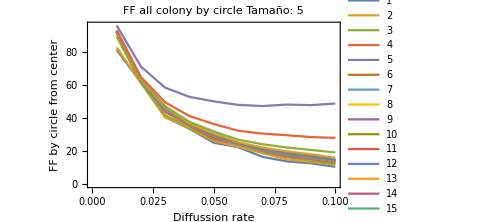
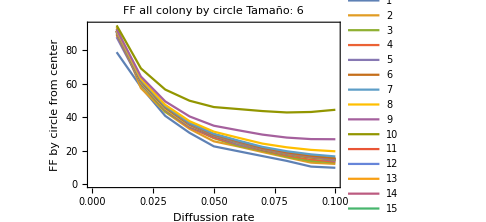

```mathematica
(*********************This effect  happens for Region 2*)
```

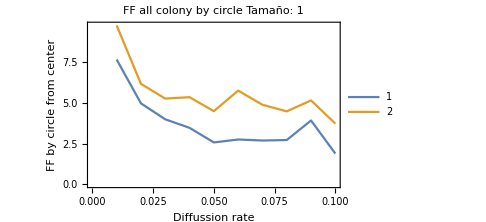
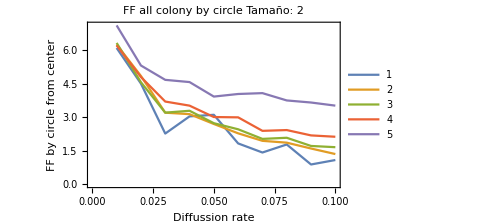
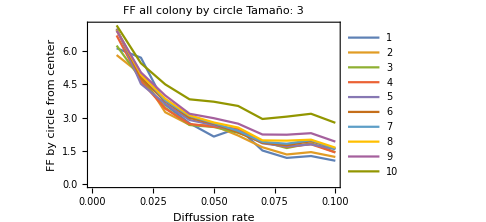
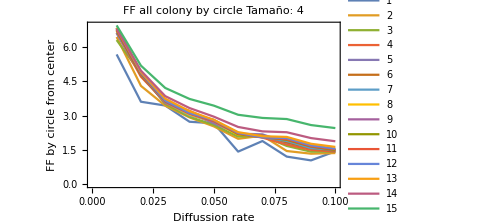
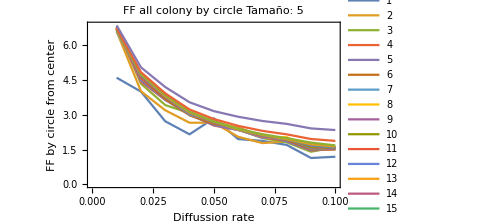
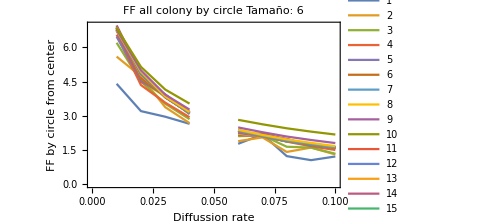

```mathematica
(*********************This effect does not happen for Region 1*)
```